```mathematica
(*Consideramos la ecuación x E^x=1. La función correspondiente a la ecuación estuadiada es f(x)=x E^x-1*)
f[x_]:=x E^x-1
```

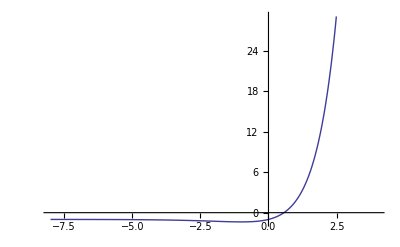

```mathematica
(*Dibujamos la gráfica de f(x) en el intervalo [-8,4]:*)
Plot[f[x],{x,-8,4}]
```

```mathematica
(*Estudiamos los intervalos de monotonía mediante los puntos críticos de f(x):*)
f1[x_]:=f'[x]
```

```mathematica
f'[x]
```

ⅇ^x+ⅇ^x x

```mathematica
Solve[f'[x]==0]
```

{{x→-1}}

```mathematica
(*La única solución de la ecuación f'(x)=0 corresponde a x=-1. Por tanto, hay solo dos intervalos de monotonía. El primero es (-∞,-1) y (-1,∞)

Veamos el cambio de signo en ambos intervalos para determinar si existe solución o no:*)
Limit[f[x],x->-Infinity]
f[-1]
Limit[f[x],x->Infinity]
```

-1

-1-1/ⅇ

∞

```mathematica
(*Los extemos de (-∞,-1) son ambos negativos y por tanto no tiene cambio de signo y la ecuación de partida no tiene solución en dicho intervalo. Como -1 tiene signo negativo y el límite en el infinito es positivo, entonces el intervalo (-1, ∞) sí presenta cambio de signo y existe una única solución en dicho intervalo.

Además, podemos reducir el intervalo a [0,1] ya que 0 y 1 tienen signos contrarios_*)
f[0]
f[1]
```

-1

-1+ⅇ